Piecewise[{{-ⅇ^((-L+x)/Rd)+ⅇ^((L+x)/Rd), x≤-L}, {2-ⅇ^((-L-x)/Rd)-ⅇ^((-L+x)/Rd), -L<x<L}, {-ⅇ^((-L-x)/Rd)+ⅇ^((L-x)/Rd), x≥L}, {0, True}}]

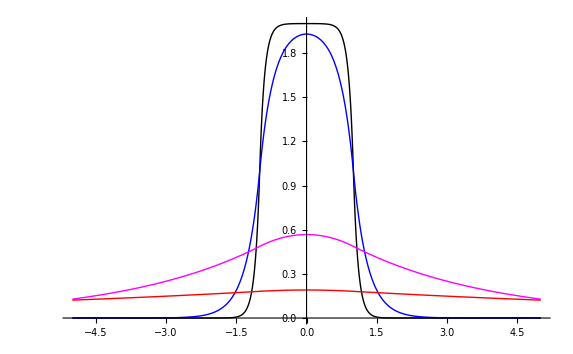

```mathematica
η[x_] = Piecewise[{{Exp[(x+L)/Rd]-Exp[(x-L)/Rd], x<=-L},
{2-Exp[-(x+L)/Rd]-Exp[(x-L)/Rd], -L < x < L}, 
{- Exp[-(x+L)/Rd]+ Exp[-(x-L)/Rd], x >= L}}] 

p1 = Plot[η[x] /. L -> 1 /.Rd -> 0.1,{x,-5 ,5}, PlotStyle->Black ];
p2 = Plot[η[x] /. L -> 1 /.Rd -> 0.3,{x,-5 ,5}, PlotStyle->Blue ];
p3 = Plot[η[x] /. L -> 1 /.Rd -> 3,{x,-5,5}, PlotStyle->Magenta ];
p4 = Plot[η[x] /. L -> 1 /.Rd -> 10,{x,-5,5}, PlotStyle->Red ];

Show[{p1, p2, p3, p4}, PlotRange -> All]
```

```mathematica
Subscript[APE, Initial] = 4 Subscript[ρ, 0] g L;
Subscript[APE, Final] = Integrate[1/2 Subscript[ρ, 0] g η[x]^2,{x,-Infinity,Infinity},    
Assumptions->{Re[Rd]>0, L>0}];
PE[a_] = FullSimplify[Subscript[APE, Final]/Subscript[APE, Initial]/.L -> (a Rd)/2, Assumptions->{Re[Rd]>0, L>0}]
```

(ⅇ^-a (3+a+(-3+2 a) ⅇ^a))/(2 a)

Here, we let a’ = 2 L / Rd, and reformat the equation.  Plot the Mathematica solution and the (further simplified) solution given in the book on the same plot to show that they are indeed identical.

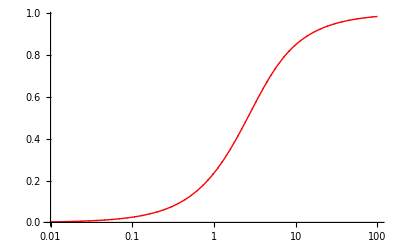

```mathematica
Subscript[PE, Book][a_] = 1-3/(2 a)+ⅇ^(- a) (1/2+3/(2 a));
p5 = LogLinearPlot[PE[a],{a,0.01,100}, PlotStyle -> {Black, Dotted, Thick}];
p6 = LogLinearPlot[Subscript[PE, Book][a],{a,0.01,100}, PlotStyle -> Red];

Show[{p5, p6}, PlotRange -> All]
```

Calculate the amount of APE that is retained when the feature is exactly 1 Rd across (i.e., 2 L = Rd, or a’ = 1).

```mathematica
PE[1.0]
PEr[1.0]
```

0.235759

0.235759